# Modelos Matemáticos de Linhas de Transmissão Análise de Sistemas de Cabos

## Aluno: Paulo Eduardo Darski Rocha Profs.: Dr. Antonio Carlos Siqueira de Lima / PhD Sandoval Carneiro Jr. Poli/COPPE/UFRJ

## Opções de programa

```mathematica
SetOptions[{ListPlot,ListLogLinearPlot,ListLogLogPlot},Axes->False,Frame->True,Joined->True,ImageSize->450,PlotStyle->{PointSize[0.015]},BaseStyle->{14,FontFamily->"Helvetica"}];
```

```mathematica
plstyle1={AbsoluteThickness[2],RGBColor[1,0,0]};
plstyle2={AbsoluteThickness[2],RGBColor[0,0,1]};
plstyle3={AbsoluteThickness[2],PointSize[.015],RGBColor[0,1,0]};
```

## Dados de Entrada

Dimensões dos cabos

```mathematica
r1=1.27 10^-2;
r2=2.82 10^-2;
r3=2.93 10^-2;
r4=3.45 10^-2;
```

Constantes Elétricas e Parâmetros do Solo por metro

```mathematica
compr=10*10^3;
μ=4.0 π 10^-7;
ϵ=8.854*10^-12;
ϵcs=3.5;
ϵsg=3.3;
ϵ1=ϵcs ϵ;
ϵ2=ϵsg ϵ;
ρs=1.38 10^-7;
ρc=1.72 10^-8;
ρ=20.0;
```

## Configuração da Rede

Espaçamento dos condutores

```mathematica
x1=0;x3=0.3;x5=0.6;
xc={x1,x1,x3,x3,x5,x5};
hc={1.0,1.0,1.0,1.0,1.0,1.0};
r={r1,r4,r1,r4,r1,r4};
```

```mathematica
mostra=Table[{Circle[{xc[[i]],-hc[[i]]},r[[i]]]},{i,1,6}];
```

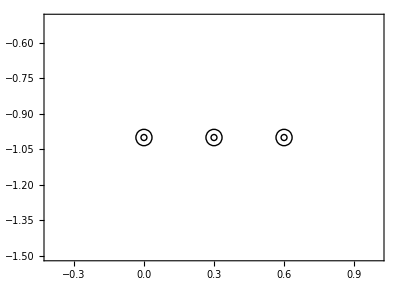

```mathematica
Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->True,PlotRange->{{-0.4,1},{-1.5,-0.5}}]
```

S_ij é a distância entre o cabo  i e  j, d é a soma  das profundidades do cabo i para  o cabo j

```mathematica
s13=.30;
s35=s13;
s15=2*s13;
```

Espaçamento dos condutores

```mathematica
d=√((x1-x3)^2+(hc[[1]]-hc[[3]])^2);
Dc=√((x1-x3)^2+(hc[[1]]+hc[[3]])^2);
d15=√((x1-x5)^2+(hc[[1]]-hc[[3]])^2);
Dc15=√((x1-x5)^2+(hc[[1]]+hc[[5]])^2);
```

## Frequências e Inicialização das Listas

### Freqüências de interesse

#### Faixa de Frequência

```mathematica
freq[i_,f_,n_]:=Table[N[10^(i+x(f-i)/(Floor[n]-1))],{x,0,n-1}]
ndecadas=6;
npontos=20;
nfd=ndecadas*npontos;
d1=1;d2=6;
 f=freq[d1,d2,nfd];
```

```mathematica
nf=Length[f]
```

120

### Inicialização das listas

```mathematica
T=Table[0,{n,1,nf}];
T1=Table[0,{n,1,nf}];
λ=Table[0,{n,1,nf}];
λ0=Table[0,{n,1,nf}];
Γ1=Table[0,{n,1,nf}];
Yc1=Table[0,{n,1,nf}];
Af1=Table[0,{n,1,nf}];
Am1=Table[0,{n,1,nf}];
Zcabo=Table[0,{n,1,nf}];
Ycabo=Table[0,{n,1,nf}];
γm=Table[0,{n,1,nf}];
S=Table[0,{n,1,nf}];
```

## 1.ba Trabalho - COM CRUZAMENTO DE AUTOVETORES

### Descruzamento de Autovetores

```mathematica
eigNR[G_?MatrixQ,V0_,d0_,Tol_: 10^-10]:=Module[{A=G,nc,scale,v,d,vec,res,jac,i},nc=Length[A];
scale=Norm[A];
A=A/scale;
outd=Table[0,{nc}];
outv=Table[0,{nc},{nc}];
itr=0;
jac=Table[0.0,{nc+1},{nc+1}];
Do[{v=V0[[1;;,i]];
d=d0[[i]];
res=Max[Abs[A.v-v*d]];
While[res>Tol,itr=itr+1;
jac[[1;;nc,1;;nc]]=A-d*IdentityMatrix[nc];
jac[[1;;nc,nc+1]]=-v;
jac[[nc+1,1;;nc]]=2*v;
res=Join[A.v-v*d,{v.v-1}];
vec=LinearSolve[jac,res];
res=Max[Abs[vec]];
v=v-vec[[1;;nc]];
d=d-vec[[nc+1]];];
outd[[i]]=d*scale;
outv[[1;;,i]]=v;},{i,1,nc}]];
```

### Rotina

```mathematica
AbsoluteTiming[Do[{ω=2 π f[[nm]],
ηc=√((ⅉ  ω μ)/ρc),
ηs=√((ⅉ  ω μ)/ρs),
η=√((ⅉ  ω μ)/ρ),
(*-----------Matrix de Admitância-Shunt-------------*)
y1=ⅉ ω 2 π ϵ1/Log[r2/r1],
y2=ⅉ ω 2 π ϵ2/Log[r4/r3],
Ycond={{y1, -y1},{-y1, y1+y2}},
Zero=Table[0,{i,1,2},{j,1,2}],
Ycabo[[nm]]=ArrayFlatten[{{Ycond,Zero,Zero},{Zero,Ycond,Zero},{Zero,Zero,Ycond}}],

(*----------Matriz de Impedância Série--------------*)
z1=(ρc ηc)/(2π r1)BesselI[0,ηc r1]/BesselI[1,ηc r1],
z2=ⅉ(ω μ)/(2π)Log[r2/r1],
z6=ⅉ(ω μ)/(2π)Log[r4/r3],
Den=BesselI[1,ηs r3]BesselK[1,ηs r2]-BesselI[1,ηs  r2]BesselK[1,ηs r3],
z3=(ρs ηs)/(2π r2)1/Den(BesselI[0,ηs r2]BesselK[1, ηs r3]+BesselK[0,ηs  r2]BesselI[1,ηs  r3]),
z4=ρs/(2π r2 r3)1/Den,
z5=(ρs ηs)/(2π r3)1/Den(BesselI[0,ηs r3]BesselK[1, ηs r2]+BesselK[0,ηs r3]BesselI[1,ηs r2]),
z7=ⅉ(ω μ)/(2π)(-Log[(EulerGamma η r4)/2]+1/2-(4η)/3 hc[[1]]),
zsolo1=Table[(ⅉ ω μ)/(2π)(-Log[(EulerGamma η  s13)/2]+1/2-(2η)/3 d),{i,1,2},{j,1,2}],
zsolo2=Table[(ⅉ ω μ)/(2π)(-Log[(EulerGamma η   s15)/2]+1/2-(2η)/3 d),{i,1,2},{j,1,2}],
Zint={{z1+z2+z3+z5+z6+z7-2 z4,z5+z6+z7-z4},{z5+z6+z7-z4,z5+z6+z7}},
Zcabo[[nm]]=ArrayFlatten[{{Zint,zsolo1,zsolo2},{zsolo1,Zint,zsolo1},{zsolo2,zsolo1,Zint}}],
S[[nm]]=Zcabo[[nm]].Ycabo[[nm]],
{eval,evect}=Eigensystem[Zcabo[[nm]].Ycabo[[nm]]],
{eval0,evect0}=Eigensystem[Zcabo[[1]].Ycabo[[1]]],
d0=DiagonalMatrix[eval0],
V0=Transpose[evect0],
eigNR[S[[nm]],V0,d0],
T[[nm]]=outv,
λ[[nm]]=outd
(*λ[[nm]]=outd,
γm[[nm]]=Sqrt[λ[[nm]]],
Delt=Exp[-γm[[nm]] compr],
Am1[[nm]]=Γ,
Af1[[nm]]=T[[nm]].DiagonalMatrix[Delt].Inverse[T[[nm]]]*)
},{nm,1,nf}]]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-0.0000106252 + 5.66618×10^-6\ ⅈ, -0.30133 + 0.0539941\ ⅈ, 0.  + 0.\ ⅈ, « 1 », 0.  + 0.\ ⅈ, -0.17057 + 0.0415493\ ⅈ, 0.707107  + 7.00618×10^-9\ ⅈ}, « 6 »} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-8.12437×10^-6 + 5.95083×10^-6\ ⅈ, -0.301531 + 0.0553147\ ⅈ, 0.  + 0.\ ⅈ, -« 20 » + « 21 »\ ⅈ, 0.  + 0.\ ⅈ, -0.16993 + 0.0421255\ ⅈ, 0.707107  + 7.16588×10^-9\ ⅈ}, « 5 », {« 1 »}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-5.93893×10^-6 + 5.88582×10^-6\ ⅈ, -0.301714 + 0.0567026\ ⅈ, 0.  + 0.\ ⅈ, -« 20 » + « 20 »\ ⅈ, 0.  + 0.\ ⅈ, -0.169276 + 0.0427219\ ⅈ, -0.572458 + 0.000423874\ ⅈ}, « 5 », {« 1 »}} may contain significant numerical errors.

General::stop: Further output of LinearSolve :: "luc" will be suppressed during this calculation.

{6.442806,Null}

```mathematica
λ//Dimensions
```

{120,6,6}

```mathematica
col=2;
```

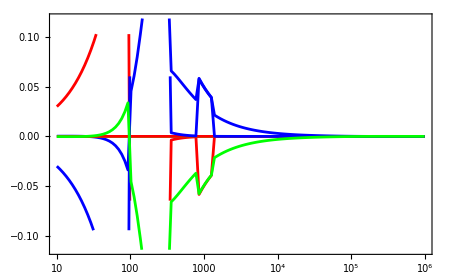

```mathematica
a1=ListLogLinearPlot[Transpose[{f,Im[T[[Range[nf],1,col]]]}],PlotStyle->plstyle1, DisplayFunction->Identity];
a2=ListLogLinearPlot[Transpose[{f,Im[T[[Range[nf],2,col]]]}],PlotStyle->plstyle2, DisplayFunction->Identity];
a3=ListLogLinearPlot[Transpose[{f,Im[T[[Range[nf],3,col]]]}],PlotStyle->plstyle3, DisplayFunction->Identity];
a4=ListLogLinearPlot[Transpose[{f,Im[T[[Range[nf],4,col]]]}],PlotStyle->plstyle1, DisplayFunction->Identity];
a5=ListLogLinearPlot[Transpose[{f,Im[T[[Range[nf],5,col]]]}],PlotStyle->plstyle2, DisplayFunction->Identity];
a6=ListLogLinearPlot[Transpose[{f,Im[T[[Range[nf],6,col]]]}],PlotStyle->plstyle3, DisplayFunction->Identity];
Pla1=Show[{a1,a2,a3,a4,a5,a6},PlotRange-> All]
```

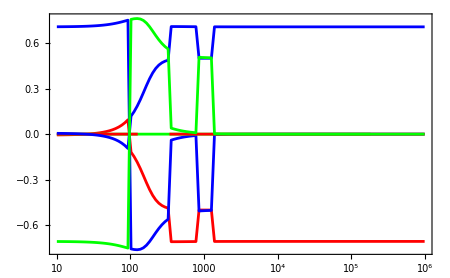

```mathematica
b1=ListLogLinearPlot[Transpose[{f,Re[T[[Range[nf],1,col]]]}],PlotStyle->plstyle1, DisplayFunction->Identity];
b2=ListLogLinearPlot[Transpose[{f,Re[T[[Range[nf],2,col]]]}],PlotStyle->plstyle2, DisplayFunction->Identity];
b3=ListLogLinearPlot[Transpose[{f,Re[T[[Range[nf],3,col]]]}],PlotStyle->plstyle3, DisplayFunction->Identity];
b4=ListLogLinearPlot[Transpose[{f,Re[T[[Range[nf],4,col]]]}],PlotStyle->plstyle1, DisplayFunction->Identity];
b5=ListLogLinearPlot[Transpose[{f,Re[T[[Range[nf],5,col]]]}],PlotStyle->plstyle2, DisplayFunction->Identity];
b6=ListLogLinearPlot[Transpose[{f,Re[T[[Range[nf],6,col]]]}],PlotStyle->plstyle3, DisplayFunction->Identity];
Plb1=Show[{b1,b2,b3,b4,b5,b6},PlotRange-> All]
```